```mathematica
Clear["Global`*"];
```

```mathematica
<</home/xierr/.Mathematica/Applications/CustomTicks/CustomTicks.m
```

```mathematica
tlen=0.014;tickd=In;thick=Thickness[0.002];ip={{80,30},{60,30}};
```

```mathematica
cliprange[points_List,xmax_:4.99]:=Module[{xmaxpos},xmaxpos=Position[points,Nearest[points[[All,1]],xmax][[1]]][[1,1]];
points[[1;;xmaxpos]]];
```

```mathematica
(*NND fitting formular*) 
ξsb[ξb_?NumericQ]:=Gamma[ξb+1/2]/Gamma[ξb];
pp[s_,ξb_]:=1/Gamma[1/2+ξb]^2 2^(-1-2 ξb) Gamma[ξb] Gamma[2+2 ξb] HypergeometricU[1+ξb,1/2,(s^2 Gamma[ξb]^2)/(4 Gamma[1/2+ξb]^2)];
```

```mathematica
nnd1=cliprange[Import["A2ASS6_NND.txt","Table"]];
nnd2=cliprange[Import["Q8WXI7_NND.txt","Table"]];
nnd3=cliprange[Import["Q8WZ42_NND.txt","Table"]];
nnd4=cliprange[Import["Q9I7U4_NND.txt","Table"]];
```

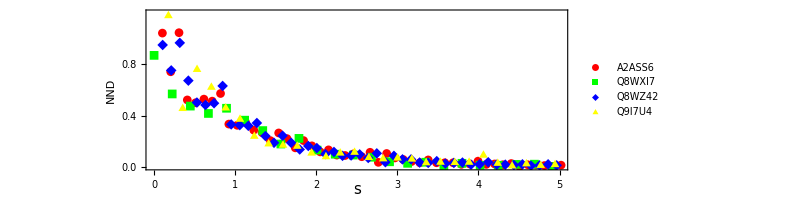

```mathematica
nndpoints=ListPlot[{nnd1,nnd2,nnd3,nnd4}(*use your data*),PlotRange->{{0,5},{0,1.2}},AspectRatio->1/3.,ImageSize->600,PlotMarkers->Automatic,Frame->True,PlotStyle->{Red, Green, Blue, Yellow},
(*********************Frame Ticks***********************)
ImagePadding->ip,PlotRangeClipping->False,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[{0,0.2,0.4,0.6,0.8,1},{0.1,0.3,0.5,0.7,0.9,1.1},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,TickDirection->tickd],(*left*)
LinTicks[{0,0.2,0.4,0.6,0.8,1},{0.1,0.3,0.5,0.7,0.9,1.1},MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[{0,1,2,3,4,5},{0.5,1.5,2.5,3.5,4.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],(*down*)
LinTicks[{0,1,2,3,4,5},{0.5,1.5,2.5,3.5,4.5},MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}},(*up*)FrameLabel->{None,Style["NND",FontFamily->"Times",Italic,15]},
(***************************************)PlotLegends->Placed[PointLegend[Automatic,Style[#,12,FontFamily->"Times"]&/@{"A2ASS6","Q8WXI7","Q8WZ42","Q9I7U4"},LegendFunction->Framed,LegendMargins->0],{(*legend position*)Scaled[0.85],Scaled[0.5]}],Epilog->{Text[Style["StyleBox[\"s\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times"],Scaled[{0.5,-0.12}]]}]
```

```mathematica
nlm1=NonlinearModelFit[nnd1,pp[s,ξb],ξb,s]
```

FittedModel[6.57497 HypergeometricU[«18»,«1»,«20» «1»]]

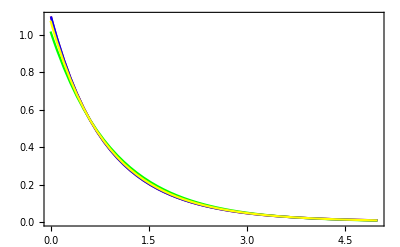

```mathematica
nndmat=Plot[{pp[s,2.441],pp[s,13.124],pp[s,2.415],pp[s,3.365]},{s,0,5},PlotRange->{{0,5},{0,1.1}},PlotStyle->{Red, Green, Blue, Yellow},Frame->True]
```

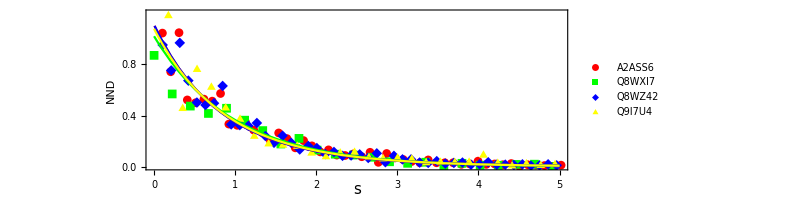

```mathematica
p1=Show[nndpoints,nndmat]
```

```mathematica
NV[L_?NumericQ,ξb_?NumericQ]:= L+((ξsb[ξb]/(√ξb))^-2-1) L^2;
```

```mathematica
nv1=Import["A2ASS6_variance.txt","Table"];
nv2=Import["Q8WXI7_variance.txt","Table"];
nv3=Import["Q8WZ42_variance.txt","Table"];
nv4=Import["Q9I7U4_variance.txt","Table"];
```

```mathematica
nvpoints=ListPlot[{nv1,nv2,nv3,nv4}(*use your data*),PlotRange->{{0,225},{0,4500}},DataRange->{{0,225},{0,4500}},AspectRatio->1/3.(*specify the height-to-width ratio*),ImageSize->600,PlotMarkers->Automatic,Frame->True,PlotStyle->{Red, Green, Blue, Yellow},
(*********************Frame Ticks***********************)
ImagePadding->ip,FrameStyle->Directive[thick,Black,FontSize->20,FontFamily->"Times"],FrameTicksStyle->Directive[thick,"Label", 15],FrameTicks->{{LinTicks[Range[0,4000,1000],Range[500,4500,500],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->True,TickDirection->tickd],(*left*)
LinTicks[Range[0,4000,1000],Range[500,4500,500],MajorTickLength->2tlen,MinorTickLength->tlen,ShowFirst->False,TickDirection->tickd,ShowTickLabels->False]},(*right*){LinTicks[Range[0,200,50],Range[25,225,25],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->True],(*down*)
LinTicks[Range[0,200,50],Range[25,225,25],MajorTickLength->2tlen,MinorTickLength->tlen,TickDirection->tickd,ShowTickLabels->False]}},(*up*)FrameLabel->{Style["StyleBox[\"L\",FontSlant->\"Italic\"]",FontSize->15,FontFamily->"Times"],Style["NV",FontFamily->"Times",Italic,15]}];
```

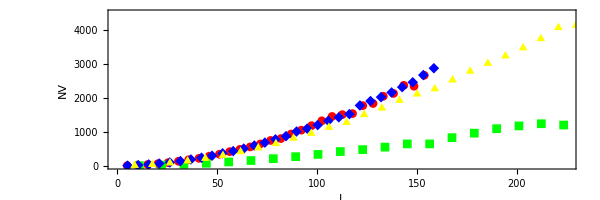

```mathematica
Show[nvpoints]
```

```mathematica
nlm1=NonlinearModelFit[nv1,NV[L,ξb],ξb,L];
nlm2=NonlinearModelFit[nv2,NV[L,ξb],ξb,L];
nlm3=NonlinearModelFit[nv3,NV[L,ξb],ξb,L];
nlm4=NonlinearModelFit[nv4,NV[L,ξb],ξb,L];
```

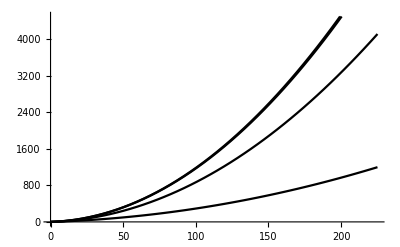

```mathematica
nvcurv=Plot[{Normal[nlm1],Normal[nlm2],Normal[nlm3],Normal[nlm4]},{L,0,225},PlotStyle->Black,PlotRange->{{0,225},{0,4500}}]
```

```mathematica
p3=Show[nvpoints,nvcurv,(*we want nvcurv as background*)Epilog->{Text[Style["λ = 2.441",FontSize->13,FontFamily->"Times"],Scaled[{0.4,0.53}]],
Line[{Scaled[{0.4,0.5}],Scaled[{0.45,0.3}]}],
Text[Style["λ = 13.124",FontSize->13,FontFamily->"Times"],Scaled[{0.9,0.1}]],
Text[Style["λ = 2.415",FontSize->13,FontFamily->"Times"],Scaled[{0.65,0.8}]],
Text[Style["λ = 3.365",FontSize->13,FontFamily->"Times"],Scaled[{0.78,0.32}]],
Line[{Scaled[{0.58,0.3}],Scaled[{0.7,0.25}]}]}]
```

-Graphics-

```mathematica
p=Column[{p1,p3},Spacings->-4.5]
```

-Graphics-

```mathematica
Export["Protein_new.eps",p]
```

Protein_new.eps